```mathematica
rhob=1232846739.44207``20
Nb=rhob/mb
myye=0.4376794000579805``20
myye=0.5``20
```

1.23284673944207×10^9

7.42437×10^32

0.4376794000579805

0.5

```mathematica
f[k_,eta_,beta_]:=x^k*(1+beta*x/2)^(1/2)/(Exp[x-eta]+1)
F[k_,eta_,beta_]:=NIntegrate[f[k,eta,beta],{x,0,Infinity},WorkingPrecision->30]
(*F[k_,eta_,beta_]:=NIntegrate[f[k,eta,beta],{x,0,Infinity}];*)
Nele[eta_,beta_]:=8*Pi*Sqrt[2]/h^3*me^3*c^3*beta^(3/2)*(F[1/2,eta,beta]+beta*F[3/2,eta,beta])
Npos[eta_,beta_]:=8*Pi*Sqrt[2]/h^3*me^3*c^3*beta^(3/2)*(F[1/2,-eta-2/beta,beta]+beta*F[3/2,-eta-2/beta,beta])
Ntot[eta_,beta_]:=Nele[eta,beta]+Npos[eta,beta]
Pele[eta_,beta_]:=16*Pi*Sqrt[2]/3/h^3*me^4*c^5*beta^(5/2)*(F[3/2,eta,beta]+1/2*beta*F[5/2,eta,beta])
Ppos[eta_,beta_]:=16*Pi*Sqrt[2]/3/h^3*me^4*c^5*beta^(5/2)*(F[3/2,-eta-2/beta,beta]+1/2*beta*F[5/2,-eta-2/beta,beta])
Ptot[eta_,beta_]:=Pele[eta,beta]+Ppos[eta,beta]
Uele[eta_,beta_]:=8*Pi*Sqrt[2]/h^3*me^4*c^5*beta^(5/2)*(F[3/2,eta,beta]+beta*F[5/2,eta,beta])
Upos[eta_,beta_]:=8*Pi*Sqrt[2]/h^3*me^4*c^5*beta^(5/2)*(F[3/2,-eta-2/beta,beta]+beta*F[5/2,-eta-2/beta,beta])+(2*me*c^2)*Npos[eta,beta]
Utot[eta_,beta_]:=Uele[eta,beta]+Upos[eta,beta]
Sele[eta_,beta_]:=(Pele[eta,beta]+Uele[eta,beta])/(beta*(me*c^2))-eta*Nele[eta,beta]
Spos[eta_,beta_]:=(Ppos[eta,beta]+Upos[eta,beta])/(beta*(me*c^2))-(-eta-2/beta)*Npos[eta,beta]
Stot[eta_,beta_]:=Sele[eta,beta]+Spos[eta,beta]
Ye[eta_,beta_]:=(Nele[eta,beta]-Npos[eta,beta])/Nb
```

```mathematica
(* AccuracyGoal->14,PrecisionGoal->14,WorkingPrecision->100*)
```

```mathematica
Ee=Sqrt[p^2+(me*c^2)^2];
fd[EN_,eta_,beta_]:=1/(Exp[EN/(beta*(me*c^2))-eta]+1)
Nelek[eta_,beta_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[p^2*fd[Ee,eta,beta],{p,0,Infinity},WorkingPrecision->30]
Nposk[eta_,beta_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[p^2*fd[Ee,-eta,beta],{p,0,Infinity},WorkingPrecision->30]
Ntotk[eta_,beta_]:=Nelek[eta,beta]+Nposk[eta,beta]
Nek[eta_,beta_]:=Nelek[eta,beta]-Nposk[eta,beta]
Pelek[eta_,beta_]:=(1/3)*1/(Pi^2*(hbar*c)^3)*NIntegrate[p^4/Ee*fd[Ee,eta,beta],{p,0,Infinity},WorkingPrecision->30]
Pposk[eta_,beta_]:=(1/3)*1/(Pi^2*(hbar*c)^3)*NIntegrate[p^4/Ee*fd[Ee,-eta,beta],{p,0,Infinity},WorkingPrecision->30]
Ptotk[eta_,beta_]:=Pelek[eta,beta]+Pposk[eta,beta]
Uelek[eta_,beta_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[p^2*Ee*fd[Ee,eta,beta],{p,0,Infinity},WorkingPrecision->30]
Uposk[eta_,beta_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[p^2*Ee*fd[Ee,-eta,beta],{p,0,Infinity},WorkingPrecision->30]
Utotk[eta_,beta_]:=Uelek[eta,beta]+Uposk[eta,beta]
Stotk[eta_,beta_]:=(Utotk[eta,beta]+Ptotk[eta,beta])/(beta*(me*c^2)) - Nek[eta,beta]*eta
Yek[eta_,beta_]:=(Nelek[eta,beta]-Nposk[eta,beta])/Nb
```

```mathematica
betatest=0.01``20;
(*etaetest=-1/betatest;*)
(*etaetest=-1/betatest;*)
etaetest=1
etaektest=etaetest+1/betatest
nele=Nele[etaetest,betatest]
npos=Npos[etaetest,betatest]
nelek=Nelek[etaektest,betatest]
nposk=Nposk[etaektest,betatest]
Print["Diffn"];
nele-npos
(nelek-nposk)
pit=Sqrt[EN^2-m^2]
dpit=D[pit,EN]
factor=pit^2*dpit//.{EN->Sqrt[x+m^2]}
```

1

101.

NIntegrate::precw: The precision of the argument function (√1 + 0.005`18. x √x/1 + ⅇ^-1 + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + 0.005`18. x x^3/2/1 + ⅇ^-1 + x) is less than WorkingPrecision (30.).

3.55791×10^27

NIntegrate::precw: The precision of the argument function (√1 + 0.005`18. x √x/1 + ⅇ^201.`18.00216606175651 + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + 0.005`18. x x^3/2/1 + ⅇ^201.`18.00216606175651 + x) is less than WorkingPrecision (30.).

1.14386×10^-60

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^-101.`18.004321373782645 + 1.2214330650884135`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.10964755969747456188594751818×10^-21 and 5.79784183631371335324949490123×10^-28 for the integral and error estimates.

3.55791×10^27

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^101.`18.004321373782645 + 1.2214330650884135`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 3.56748798457112983779650153646×10^-109 and 1.20159525213756271880714434541×10^-117 for the integral and error estimates.

1.14386×10^-60

Diffn

3.55791×10^27

3.55791×10^27

√(EN^2-m^2)

EN/(√(EN^2-m^2))

√x √(m^2+x)

p^2/(1+ⅇ^(-101.+1.22143×10^8 √(6.70287×10^-13+p^2)))

General::ovfl: Overflow occurred in computation.

Underflow[]

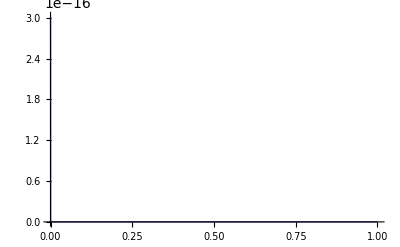

```mathematica
func=p^2*fd[Ee,etaektest,0.01]
func//.{p->10}
Plot[func,{p,0,1}]
```

```mathematica
(* So problem for Kaz expression at low beta *)
```

```mathematica
betatest=1
(*betatest=10^(13)*kb/(me*c^2)*)
etaetest=6.8``20
etaektest=etaetest+1/betatest
Ye[etaetest,betatest]
Yek[etaektest,betatest]
```

1

6.8

7.8

NIntegrate::precw: The precision of the argument function (√1 + x/2 √x/1 + ⅇ^-6.8`20.83250891270624 + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + x/2 x^3/2/1 + ⅇ^-6.8`20.83250891270624 + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + x/2 √x/1 + ⅇ^8.8`20.944482672150173 + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.426503

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^-7.8`20.892094602690484 + 1.2214330650884137`*^6 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {8.98118713567461325870186939657`30.*^-6}. NIntegrate obtained 9.87583769714343089796852959584×10^-17 and 6.25594319328651532564578449457×10^-24 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^7.8`20.892094602690484 + 1.2214330650884137`*^6 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {8.98118713567461325870186939657`30.*^-6}. NIntegrate obtained 3.65334289897571612883616875712×10^-22 and 2.86126902779057624057755520656×10^-38 for the integral and error estimates.

0.426503

```mathematica
betatest=.01
sol=FindRoot[Ye[eta,betatest]==myye,{eta,1}]
solk=FindRoot[Yek[etak,betatest]==myye,{etak,1}]
```

0.01

NIntegrate::precw: The precision of the argument function (√1 + 0.005` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00500000000000000010408340855861`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.005` x x^3/2/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00500000000000000010408340855861`30. x x^3/2/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.005` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand √1 + 0.00500000000000000010408340855861`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 3259.59974476896011605997310841 and 1.23819860560967688540087624291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 490786.461147169011092691124981 and 293.995542814145999145237072887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {252.867835328172851982720151516`30.}. NIntegrate obtained 24.2479358256680439132410519483 and 13.3020037382363161168576680699 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{eta→765.36}

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^-etak + 1.2214330650884135`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^-etak + 1.22143306508841350674629211426`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^etak + 1.2214330650884135`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^etak + 1.22143306508841350674629211426`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^etak + 1.2214330650884135`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^etak + 1.22143306508841350674629211426`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 9.58982560454875105671193828543×10^-66 and 3.23002879479586371430181939901×10^-74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 7.08597593709722589118547579822×10^-65 and 2.38668639659079944751763827599×10^-73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 7.08597593709713813139503047507×10^-65 and 2.38668639659076219776329522232×10^-73 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{etak→1.}

```mathematica
(* etak not well-converged for Kaz approach to integrals --> stays at 1 *)
```

```mathematica
myeta=sol[[1,2]]
myetak=solk[[1,2]]
myeta - (myetak-1/betatest)
```

4.21931

1.33716×10^-8

5.21931

```mathematica
ErrorM[A_,B_]:=(A-B)/(Abs[A]+Abs[B])
```

```mathematica
ErrorM[1,1]
```

0

```mathematica
(* So agrees *)
```

```mathematica
betacrap=betatest
Nele[myeta,betacrap]-Npos[myeta,betacrap]
Nelek[myetak,betacrap]-Nposk[myetak,betacrap]
```

1

NIntegrate::precw: The precision of the argument function (√1 + x/2 √x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + x/2 x^3/2/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√1 + x/2 √x/1 + ⅇ^6.2193147519191365`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

1.09062×10^32

6.67827×10^22

```mathematica
ErrorM[Nele[myeta,betatest],Nelek[myetak,betatest]]
ErrorM[Npos[myeta,betatest],Nposk[myetak,betatest]]
ErrorM[Ntot[myeta,betatest],Ntotk[myetak,betatest]]
```

NIntegrate::precw: The precision of the argument function (√x √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

-0.96797

NIntegrate::precw: The precision of the argument function (√x √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

-0.96797

NIntegrate::precw: The precision of the argument function (√x √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√x √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-0.96797

```mathematica
(* So also agrees! *)
```

```mathematica
ErrorM[Uele[myeta,betatest],Uelek[myetak,betatest]]
ErrorM[Upos[myeta,betatest],Uposk[myetak,betatest]]
ErrorM[Utot[myeta,betatest],Utotk[myetak,betatest]]
Utotknorest=(Utotk[myetak,betatest]-Nek[myetak,betatest]*(me*c^2));
ErrorM[Utot[myeta,betatest],Utotknorest]
```

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

0.938267

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (√x √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-0.969452

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.880287

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.880287

```mathematica
(* So Utot with correction agrees! *)
```

```mathematica
ErrorM[Pele[myeta,betatest],Pelek[myetak,betatest]]
ErrorM[Ppos[myeta,betatest],Pposk[myetak,betatest]]
ErrorM[Ptot[myeta,betatest],Ptotk[myetak,betatest]]
```

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

0.938275

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

-0.969458

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^5/2 √1 + 843.1906663894194` x/1 + ⅇ^-4.2193147519191365` + x) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (x^3/2 √1 + 843.1906663894194` x/1 + ⅇ^4.220500723301247`  + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.880302

```mathematica
(* So all the pressures including individuals agree, like N's *)
```

```mathematica
Stot[myeta,betatest]
Stotk[myetak,betatest]
stupid=Nek[myetak,betatest]*(me*c^2)/(betatest*me*c^2)
ErrorM[Stot[myeta,betatest],Stotk[myetak,betatest]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 125.066 and 0.000200501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 782.427 and 0.00108668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 125.066 and 0.000200501 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

4.18819×10^32

4.18817×10^32

3.71265×10^32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 125.066 and 0.000200501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 782.427 and 0.00108668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {9.092037025163762`}. NIntegrate obtained 125.066 and 0.000200501 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

1.76489×10^-6

```mathematica
(* Check monotonicity *)
```

```mathematica
theeta[beta_]:=FindRoot[Ye[eta,beta]==myye,{eta,1},WorkingPrecision->30,MaxIterations->1000][[1,2]];
```

```mathematica
Stotfinal[beta_]:=Stot[theeta[beta],beta];
SStotfinal[beta_]:=Stot[theeta[beta],beta]/Nb;
```

```mathematica
Clear[betaT,lbetaT]
```

```mathematica
NN=50
lT[i_]:=5 + (13-5)/(NN-1)*i
betaT[i_]:=kb*10^(lT[i])/(me*c^2);
(*lbetaT[lT_]:=lT + Log[10,kb] - Log[10,me*c^2];*)
```

50

```mathematica
Table[betaT[i],{i,0,NN-1}]/kb*me*c^2
```

{100000.,145635.,212095.,308884.,449843.,655129.,954095.,1.3895×10^6,2.02359×10^6,2.94705×10^6,4.29193×10^6,6.25055×10^6,9.10298×10^6,1.32571×10^7,1.9307×10^7,2.81177×10^7,4.09492×10^7,5.96362×10^7,8.68511×10^7,1.26486×10^8,1.84207×10^8,2.6827×10^8,3.90694×10^8,5.68987×10^8,8.28643×10^8,1.20679×10^9,1.75751×10^9,2.55955×10^9,3.72759×10^9,5.42868×10^9,7.90604×10^9,1.1514×10^10,1.67683×10^10,2.44205×10^10,3.55648×10^10,5.17947×10^10,7.54312×10^10,1.09854×10^11,1.59986×10^11,2.32995×10^11,3.39322×10^11,4.94171×10^11,7.19686×10^11,1.04811×10^12,1.52642×10^12,2.223×10^12,3.23746×10^12,4.71487×10^12,6.86649×10^12,1.×10^13}

```mathematica
theetak[beta_]:=FindRoot[Yek[eta,beta]==myye,{eta,1},WorkingPrecision->30,MaxIterations->1000][[1,2]];
godetak=theetak[betaT[16]]
Stotk[godetak,betaT[16]]/Nb
```

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^-eta + 1.768760326270993`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^-eta + 1.76876032627099305391311645508`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^eta + 1.768760326270993`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^eta + 1.76876032627099305391311645508`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (p^2/1 + ⅇ^eta + 1.768760326270993`*^8 √Plus[« 2 »]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand p^2/1 + 2.71828182845904523536028747135`30.^eta + 1.76876032627099305391311645508`30.*^8 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-3.206342379440595`*^48 NIntegrate[p^2 fd[Ee, Times[« 2 »], 0.006905588320513228`], {p, 0, ∞}, WorkingPrecision → 30] + 3.206342379440595`*^48 NIntegrate[p^2 fd[Ee, eta, 0.006905588320513228`], {p, 0, ∞}, WorkingPrecision → 30]) == 0.5`19.69897000433602) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.89350745522394072849750419962×10^-85 and 1.27109843936868387951476214237×10^-93 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.39912328103931143389617146733×10^-84 and 9.39221767575840494159355786378×10^-93 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.39912328103927693938175895025×10^-84 and 9.39221767575809821581331955405×10^-93 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

1.00000000000000000000000000006

NIntegrate::precw: The precision of the argument function (p^2 √6.702867816839887`*^-13 + p^2/1 + ⅇ^-1.000000000000000000000000000063108872417680944433`30. + 1.768760326270993`*^8 √« 1 ») is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.15744383822783865450884156434×10^-90 and 1.02920093356534649916976493668×10^-98 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (p^2 √6.702867816839887`*^-13 + p^2/1 + ⅇ^1.000000000000000000000000000063108872417680944433`30. + 1.768760326270993`*^8 √« 1 ») is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 1.56642989677036665065505081084×10^-91 and 1.3928719985145237084891337708×10^-99 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (p^4/(1 + ⅇ^-1.000000000000000000000000000063108872417680944433`30. « 1 » 1.768760326270993`*^8 « 1 » « 1 ») √6.702867816839887`*^-13 + p^2) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.13509388966478312260731265055`30.*^-7}. NIntegrate obtained 2.37305743507209224318638498779×10^-92 and 5.31658080517358064692030864611×10^-99 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

1.00543×10^-66

```mathematica
godeta=theeta[betaT[16]]
Stot[godeta,betaT[16]]/Nb
```

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x x^3/2/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x x^3/2/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-1.4279628267534793`*^27 (NIntegrate[f[1/2, Plus[« 2 »], 0.006905588320513228`], {x, 0, ∞}, WorkingPrecision → 30] + 0.006905588320513228` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]]) + 1.4279628267534793`*^27 (NIntegrate[f[1/2, eta, 0.006905588320513228`], {x, 0, ∞}, WorkingPrecision → 30] + 0.006905588320513228` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]])) == « 21 ») is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 3045.74892843365234678112045474 and 1.12942716049706236653524452308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 454721.353552206747884094971436 and 268.173306287210473818289812697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {252.867835328172851982720151516`30.}. NIntegrate obtained 22.1025790458241932989909578385 and 12.1245222929999586774995233949 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

1109.23578124346145023889591361

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x x^3/2/1 + ⅇ^-1109.23578124346145023889591360720619090771`30. + x) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {984.386024432222505106691816482`30.}. NIntegrate obtained 3.12748557882543564903121024027×10^7 and 244878.213622207384878827124082 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x x^5/2/1 + ⅇ^-1109.23578124346145023889591360720619090771`30. + x) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {984.386024432222505106691816482`30.}. NIntegrate obtained 2.5589121551392281553498868489×10^10 and 2.6545868804287178702840384331×10^8 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x x^3/2/1 + ⅇ^-1109.23578124346145023889591360720619090771`30. + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {984.386024432222505106691816482`30.}. NIntegrate obtained 3.12748557882543564903121024027×10^7 and 244878.213622207384878827124082 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-1.14738

```mathematica
SStotfinal[betaT[16]]
```

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x x^3/2/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x x^3/2/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 0.003452794160256614` x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand √1 + 0.00345279416025661388400802565002`30. x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-1.4279628267534793`*^27 (NIntegrate[f[1/2, Plus[« 2 »], 0.006905588320513228`], {x, 0, ∞}, WorkingPrecision → 30] + 0.006905588320513228` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]]) + 1.4279628267534793`*^27 (NIntegrate[f[1/2, eta, 0.006905588320513228`], {x, 0, ∞}, WorkingPrecision → 30] + 0.006905588320513228` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]])) == « 21 ») is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 3045.74892843365234678112045474 and 1.12942716049706236653524452308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 454721.353552206747884094971436 and 268.173306287210473818289812697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {252.867835328172851982720151516`30.}. NIntegrate obtained 22.1025790458241932989909578385 and 12.1245222929999586774995233949 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

```mathematica
sspectotvsbeta=Table[SStotfinal[betaT[i]],{i,0,NN-1}]
```

NIntegrate::precw: The precision of the argument function (√1 + 8.431906663894195`*^-6 x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 8.43190666389419471731143940207`30.*^-6 x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 8.431906663894195`*^-6 x x^3/2/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand √1 + 8.43190666389419471731143940207`30.*^-6 x x^3/2/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

NIntegrate::precw: The precision of the argument function (√1 + 8.431906663894195`*^-6 x √x/1 + ⅇ^-eta + x) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand √1 + 8.43190666389419471731143940207`30.*^-6 x √x/1 + 2.71828182845904523536028747135`30.^-eta + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-1.7232550304326372`*^23 (NIntegrate[f[1/2, Plus[« 2 »], 0.00001686381332778839`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00001686381332778839` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]]) + 1.7232550304326372`*^23 (NIntegrate[f[1/2, eta, 0.00001686381332778839`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00001686381332778839` « 1 »)) == 0.5`19.69897000433602) is less than WorkingPrecision (50.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-3.0286390253198246`*^23 (NIntegrate[f[1/2, Plus[« 2 »], 0.00002455958886478979`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00002455958886478979` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]]) + 3.0286390253198246`*^23 (NIntegrate[f[1/2, eta, 0.00002455958886478979`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00002455958886478979` « 1 »)) == 0.5`19.69897000433602) is less than WorkingPrecision (50.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (1.346915341177301`*^-33 (-5.322865265849449`*^23 (NIntegrate[f[1/2, Plus[« 2 »], 0.00003576731985129309`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00003576731985129309` NIntegrate[f[« 3 »], {« 3 »}, Rule[« 2 »]]) + 5.322865265849449`*^23 (NIntegrate[f[1/2, eta, 0.00003576731985129309`], {x, 0, ∞}, WorkingPrecision → 30] + 0.00003576731985129309` NIntegrate[f[« 3 »], « 1 », Rule[« 2 »]])) == « 21 ») is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 2885.77974991583241804853128219 and 1.04667104771775063455855244665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {227.139773898490940234600480024`30.}. NIntegrate obtained 427616.305834613136324960314881 and 248.527445109351579235963977061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {252.867835328172851982720151516`30.}. NIntegrate obtained 20.4692010775477281056712663611 and 11.2280012350854834530830310562 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{7.05592×10^-10,1.24012×10^-9,2.1796×10^-9,3.83087×10^-9,6.73333×10^-9,1.18352×10^-8,2.0804×10^-8,3.65722×10^-8,6.42986×10^-8,1.13063×10^-7,1.98859×10^-7,3.49876×10^-7,6.15884×10^-7,1.08492×10^-6,1.91314×10^-6,2.81183,-1.14738,0.891783,-0.232002,0.0129571,0.0180461,0.0261767,0.0381201,0.0555087,0.0808174,0.117629,0.171093,0.248516,0.359946,0.518404,0.739221,1.04376,1.53602,2.95994,8.10407,24.5401,75.2259,231.157,711.34,2191.41,6756.44,20842.9,64323.5,198564.,613076.,1.89315×10^6,5.84649×10^6,1.80564×10^7,5.57682×10^7,1.72248×10^8}

```mathematica
CForm[sspectotvsbeta]
```

List(7.055919815517668e-10,1.2401168594559556e-9,2.179599068283459e-9,3.830874597704539e-9,
   6.733330286199586e-9,1.1835249675169102e-8,2.080403303107157e-8,3.657215554008075e-8,
   6.429859746698151e-8,1.1306344031209896e-7,1.988586164390799e-7,3.498761520659816e-7,
   6.158842420342546e-7,1.0849159030911979e-6,1.9131386942718805e-6,2.811825195356003,
   -1.1473803208797961,0.8917831965413787,-0.2320016945965825,0.01295714278912186,
   0.018046121146650593,0.026176716270725955,0.03812005186461481,0.055508742334277515,
   0.08081739820751385,0.11762850101351115,0.17109349009971123,0.24851588789211418,
   0.35994623323425334,0.5184038993944239,0.7392206649801661,1.0437599274032634,
   1.5360205517906127,2.959937760458456,8.104073081155828,24.540120911262548,75.22592952263565,
   231.15671151888208,711.3398059425236,2191.4111494651347,6756.437999178434,20842.881988839843,
   64323.50175803371,198564.17598391196,613076.3887717722,1.8931506070191357e6,
   5.846485993088243e6,1.805641863490493e7,5.576822858237962e7,1.7224825148071504e8)

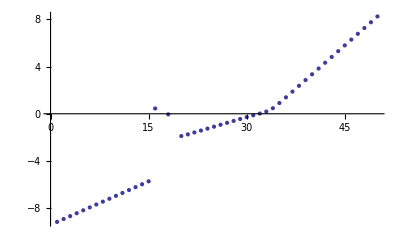

```mathematica
ListPlot[Log[10,sspectotvsbeta]]
```